```mathematica
Mac
f = Import["/Users/newlocaluser/Documents/MP2/Data/sData/sofiaNormCrossOmega.mat","LabeledData"];
bciTraits = Import["/Users/newlocaluser/Documents/MP2/Data/David Data/bci.traits.csv"];
species = Import["/Users/newlocaluser/Documents/MP2/Code/species.csv"];
class = Import["/Users/newlocaluser/Documents/MP2/Code/classification.csv"];
```

Mac

```mathematica
Windows

f=Import["C:/Users/Joel/Documents/CoMPLEX/MP2/sData/sofiaNormCrossOmega.mat","LabeledData"];
bciTraits = Import["C:/Users/Joel/Documents/CoMPLEX/MP2/bci.traits.csv"];
```

Windows

```mathematica
Data Purification
bciAdultNormCrossOmegas10 = Flatten[Values[Select[f,Keys[#]=="bciAdultNormCrossOmegas10"&]],1];
index14110 = Flatten[Values[Select[f,Keys[#]=="index141_10"&]]];
clusterIndices = Map[IntegerPart[#]&,Flatten[Values[Select[f,Keys[#]=="bciAdultClusterIndices10_5_141"&]]]];
B=MapThread[If[#2,MapThread[If[#2,#1,0]&,{#1,index14110}],ConstantArray[0,Length[#1]]]&,{bciAdultNormCrossOmegas10,index14110}];
clusterSpecies = DeleteCases[Flatten[MapIndexed[If[Length[DeleteCases[#,0]]>0,#2,0]&,B]],0];
clusters = Map[Keys[#]&,GatherBy[MapThread[#1->#2&,{clusterSpecies,clusterIndices}],Values[#]&]];
speciesMap = MapThread[#1->First[#2]&,{clusterSpecies,species}];
classMap = Select[Map[With[{ind = #},With[{class =Select[class,Values[ind]==First[#]&]},If[Length[class]>0,Keys[ind]->Last[Last[class]],Keys[ind]->0]]]&,speciesMap],Values[#]≠0&]
classClusters =Map[Keys[#]&,GroupBy[classMap,Last]]
bciTraits[[2;;All,2]];
bciValid = Flatten[Select[MapIndexed[With[{name=First[#1],index=First[#2]},index->Flatten[Select[bciTraits,MemberQ[#,name]&],1]]&,species],Values[#]≠{}&],1];
```

Data Purification

{3→S,5→U,7→T,9→U,10→M,11→T,18→T,25→T,32→T,34→T,36→T,39→U,40→T,43→M,44→M,46→T,48→M,51→M,55→U,57→S,58→T,59→T,63→M,64→U,69→T,70→M,71→M,72→U,74→U,78→U,79→T,80→U,83→T,86→U,87→M,90→U,91→M,92→M,93→U,104→M,107→T,110→M,111→T,113→U,114→M,117→M,118→U,119→M,124→M,125→T,127→U,131→T,132→M,137→M,140→M,141→T,142→U,145→U,148→M,151→T,153→T,155→M,157→M,161→U,162→M,169→M,170→S,179→M,180→T,182→T,183→M,188→S,192→U,193→M,194→U,200→U,202→T,203→T,205→T,208→T,210→T,212→M,213→M,214→M,231→T,232→U,233→U,235→S,241→T,243→U,245→M,250→S,253→T,255→*,259→T,260→T,263→U,266→T,276→M,277→T,279→M,280→U,281→M,283→M,289→M,290→T,295→M,296→S,297→T,298→T,299→T}

<|S→{3,57,170,188,235,250,296},U→{5,9,39,55,64,72,74,78,80,86,90,93,113,118,127,142,145,161,192,194,200,232,233,243,263,280},T→{7,11,18,25,32,34,36,40,46,58,59,69,79,83,107,111,125,131,141,151,153,180,182,202,203,205,208,210,231,241,253,259,260,266,277,290,297,298,299},M→{10,43,44,48,51,63,70,71,87,91,92,104,110,114,117,119,124,132,137,140,148,155,157,162,169,179,183,193,212,213,214,245,276,279,281,283,289,295},*→{255}|>

```mathematica
Graph Construction

Manipulate[
A = DeleteDuplicates[DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1>adjacencyThreshold && i≠j,i->j,0]]&,#1]]&,B]],0]];
W = DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1>adjacencyThreshold && i≠j,#1,0]]&,#1]]&,B]],0];

An = DeleteDuplicates[DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1<-adjacencyThreshold && i≠j,i->j,0]]&,#1]]&,B]],0]];
Wn = DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1< -adjacencyThreshold && i≠j,#1,0]]&,#1]]&,B]],0];
validSpecies = DeleteDuplicates[Map[Keys[#]&,A]];
validClusters = Map[Intersection[#,validSpecies]&,clusters];
gn = Graph[An,DirectedEdges->True,EdgeWeight->Abs[Wn]];
gp =Graph[A,DirectedEdges->True,EdgeWeight->W];
g = Graph[Join[An,A],DirectedEdges->True,EdgeWeight->Join[Wn,W]];
{gp,gn,g}

,{adjacencyThreshold,2.75},ControlType->InputField]
```

Construction Graph

Anton

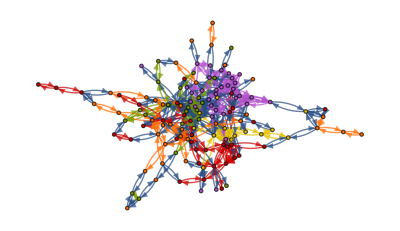

-Graphics-

{{5,10,11,18,25,39,43,45,63,90,92,93,107,112,114,121,125,127,137},{3,48,74,110,116},{6,7,17,40,46,58,69,70,131,132,140,141},{9,19,34,36,44,55,59,64,72,78,79,91,104,119},{32,57,71,83,118,124}}

```mathematica
Anton

HighlightGraph[g,Map[Subgraph[g,#]&,validClusters]]
CommunityGraphPlot[g,validClusters]
antonSpeciesClusters =Map[Intersection[Keys[bciValid],#]&,validClusters]
```

# Social Network Analysis

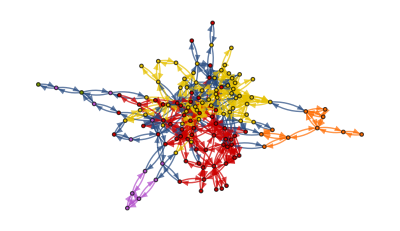

-Graphics-

```mathematica
communities = FindGraphCommunities[g,Method->"Hierarchical"];
HighlightGraph[g,Map[Subgraph[g,#]&,communities]]
CommunityGraphPlot[g,communities]
snSpeciesClusters =Map[Intersection[Keys[bciValid],#]&,communities];
```

```mathematica
ValidData[var_] := Not[MemberQ[Map[NumberQ[#]&,var],False]]
```

```mathematica
Trait Space
```

```mathematica
bciNonNullValues = DeleteCases[Map[If[ValidData[Take[#,-3]],Take[#,{6,25}],Invalid]&,Values[bciValid]],Invalid];
bciNonNullKeys = DeleteCases[Map[If[ValidData[Take[Values[#],-3]],Keys[#],Invalid]&,bciValid],Invalid];
```

```mathematica
bciData = MapThread[#2->#1&,{bciNonNullValues,bciNonNullKeys}];
```

```mathematica
reducedData = MapThread[#2->#1&,{ DimensionReduce[bciNonNullValues,3],bciNonNullKeys}];
antonClusteredReducedData = Select[MapIndexed[Flatten[#2]->Select[Map[#->Lookup[reducedData,#,Missing]&,#],Values[#]!= {}&]&,antonSpeciesClusters],Values[#]!={}&];
snClusteredReducedData = Select[MapIndexed[Flatten[#2]->Select[Map[#->Lookup[reducedData,#,Missing]&,#],Values[#]!= {}&]&,snSpeciesClusters],Values[#]!={}&];
antonCentroids = Map[Mean[#]&,Values[Values[antonClusteredReducedData]]];
snCentroids = Map[Mean[#]&,Values[Values[snClusteredReducedData]]];
classClusteredReducedData = Select[MapIndexed[Flatten[#2]->Select[Map[#->Lookup[reducedData,#,Missing]&,#],Values[#]!= {}&]&,Values[classClusters]],Values[#]!={}&];
```

```mathematica
{Anton->ListPointPlot3D[Values[Values[antonClusteredReducedData]],Axes->True,PlotTheme->"Scientific",PlotStyle->{Directive[PointSize[0.03]]}],SN->ListPointPlot3D[Values[Values[snClusteredReducedData]],Axes->True,PlotTheme->"Scientific",PlotStyle->{Directive[PointSize[0.03]]}],Classes->ListPointPlot3D[Values[Values[classClusteredReducedData]],Axes->True,PlotTheme->"Scientific",PlotStyle->{Directive[PointSize[0.03]]}]}
```

{Anton→-Graphics3D-,SN→-Graphics3D-,Classes→-Graphics3D-}

```mathematica
{Anton->ListPointPlot3D[antonCentroids,Axes->True,PlotTheme->"Detailed",PlotStyle->{Directive[PointSize[0.03]]}],SN->ListPointPlot3D[snCentroids,Axes->True,PlotTheme->"Detailed",PlotStyle->{Directive[PointSize[0.03]]}]}
```

{Anton→-Graphics3D-,SN→-Graphics3D-}

```mathematica
discreteColors[n_]:=With[{partL=Ceiling[Sqrt[n]]},DeleteCases[Flatten[Transpose[Partition[Table[Lighter[Darker[Hue[c],.1],.25],{c,0,1-1/n,1/n}],partL,partL,1,0]]],0]]
```

```mathematica
points = MapThread[{#2,Point[Values[#1]]}&,{Values[antonClusteredReducedData],discreteColors[Length[antonClusteredReducedData]]}];
labels = Map[Map[Graphics3D[Text[First[#],1.05*Last[#]]]&,Partition[Riffle[Keys[Values[#]],Values[Values[#]]],2]]&,antonClusteredReducedData];
Show[Graphics3D[PointSize[r],points],labels,PlotStyle->{Directive[PointSize[0.3]]}]
```

-Graphics3D-

# Machine Learning

```mathematica
antonLabelledData = Flatten[Map[With[{key=First[Keys[#]]},Map[Values[#]->key&,Values[#]]]&,antonClusteredReducedData]];

antonSubset = RandomSample[labelledAntonData,Round[Length[antonLabelledData]*0.75]];
antonTestSet = Complement[antonLabelledAntonData,antonSubset];
snLabelledData = Flatten[Map[With[{key=First[Keys[#]]},Map[Values[#]->key&,Values[#]]]&,snClusteredReducedData]];
snSubset = RandomSample[snLabelledData,Round[Length[snLabelledData]*0.75]];
snTestSet = Complement[snLabelledData,snSubset];
classLabelledData = Flatten[Map[With[{key=First[Keys[#]]},Map[Values[#]->key&,Values[#]]]&,classClusteredReducedData]];
classSubset = RandomSample[classLabelledData,Round[Length[classLabelledData]*0.75]];
classTestSet = Complement[classLabelledData,classSubset];
```

```mathematica
antonClassify = Classify[antonSubset,Method->"LogisticRegression"]
snClassify = Classify[snSubset,Method->"LogisticRegression"]
classClassify = Classify[classSubset,Method->"LogisticRegression"]
```

ClassifierFunction[…]

ClassifierFunction[…]

ClassifierFunction[…]

```mathematica
Mean[Map[If[Values[#]==antonClassify[Keys[#]],1,0]&,antonTestSet]]
Mean[Map[If[Values[#]==snClassify[Keys[#]],1,0]&,snTestSet]]
Mean[Map[If[Values[#]==classClassify[Keys[#]],1,0]&,classTestSet]]
```

2/11

3/11

1/2